```mathematica
SetDirectory[NotebookDirectory[]] ;
data = Import["solution22.dat"];
```

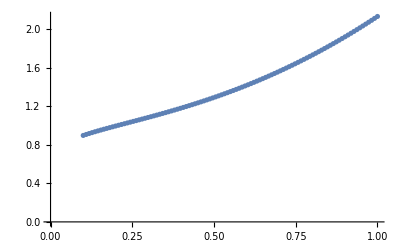

```mathematica
ListPlot[data]
```

```mathematica
eq={y[x]-λ∫_a^b k[x,s]*y[s]ⅆs==f[x]};
params = {a->0,b->1,k[x,s]->0.5(1-x *Cos[x *s]),f[x]->0.5(1+Sin[x])};
params1 = {a->0,b->1,k[x,s]->1,f[x]->0.5(1+Sin[x])};
```

```mathematica
eq=eq/.params;
DSolveValue[eq[[1]],y[x],x]
```

DSolveValue[-λ ∫_0^1 0.5 (1-x Cos[s x]) y[s]ⅆs+y[x]==0.5 (1+Sin[x]),y[x],x]